```mathematica
F1[x1_,x2_]:=(x1-1)^2+(x2-7)^2-2*x1*x2/8;
F2[x1_,x2_]:=100*(x2-x1^2)^2+(1-x1)^2;
D[F1[x1,x2],x1]
```

2 (-1+x1)-x2/4

```mathematica
D[F1[x1,x2],x2]
```

-x1/4+2 (-7+x2)

```mathematica
Plot3D[F1[x1,x2],{x1,-10,10},{x2,-10,10},ColorFunction->ColorData["BlueGreenYellow"]]
```

-Graphics3D-

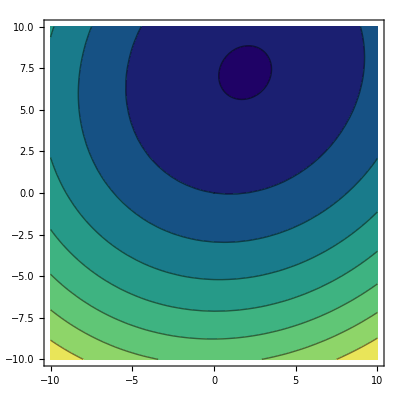

```mathematica
CP=ContourPlot[F1[x1,x2],{x1,-10,10},{x2,-10,10},ColorFunction->ColorData["BlueGreenYellow"]]
```

```mathematica
GradF1=Grad[F1[x1,x2],{x1,x2}]
```

{2 (-1+x1)-x2/4,-x1/4+2 (-7+x2)}

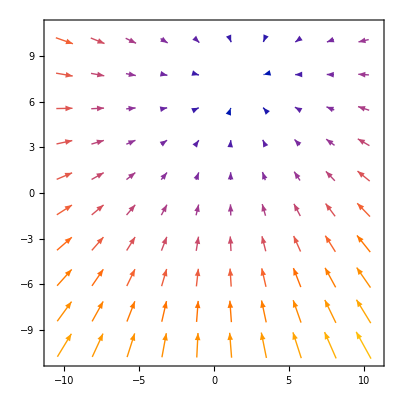

```mathematica
VP=VectorPlot[-GradF1,{x1,-10,10},{x2,-10,10},VectorScale->Automatic,ColorFunction->ColorData["BlueGreenYellow"],VectorPoints->10]
```

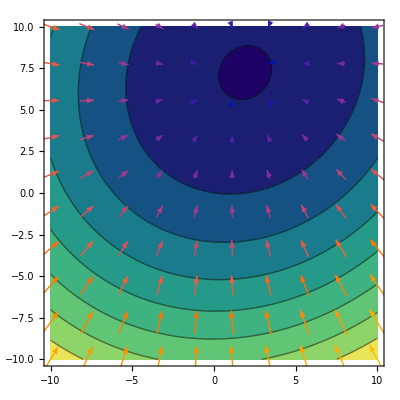

```mathematica
Show[CP,VP]
```

```mathematica
F1GradNum[x1_,x2_,dt_]:={(F1[x1+dt,x2]-F1[x1-dt,x2])/(2*dt), (F1[x1,x2+dt]-F1[x1,x2-dt])/(2*dt)};
F1GradAnalit[x1_,x2_]=Grad[F1[x1,x2],{x1,x2}];
xnum1=1;ynum1=1;dt=1;
N[F1GradNum[xnum1,ynum1,dt]]
N[F1GradAnalit[xnum1,ynum1]]
```

{-0.25,-12.25}

{-0.25,-12.25}

```mathematica
dt=0.1;
N[F1GradNum[xnum1,ynum1,dt]]
N[F1GradAnalit[xnum1,ynum1]]
```

{-0.25,-12.25}

{-0.25,-12.25}

```mathematica
dt=0.01;
N[F1GradNum[xnum1,ynum1,dt]]
N[F1GradAnalit[xnum1,ynum1]]
```

{-0.25,-12.25}

{-0.25,-12.25}

```mathematica
Plot3D[F2[x1,x2],{x1,-4,4},{x2,-4,4}]
```

-Graphics3D-

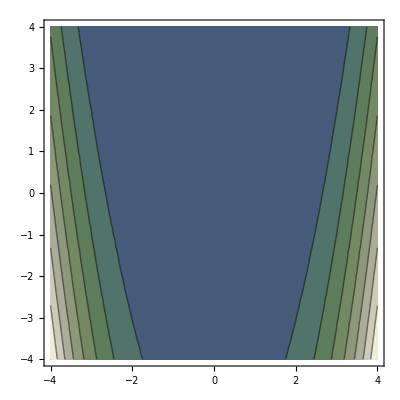

```mathematica
CP2=ContourPlot[F2[x1,x2],{x1,-4,4},{x2,-4,4},ColorFunction->ColorData["AlpineColors"]]
```

```mathematica
F2GradNum[x1_,x2_,dt_]:={(F2[x1+dt,x2]-F2[x1-dt,x2])/(2*dt), (F2[x1,x2+dt]-F2[x1,x2-dt])/(2*dt)};
F2GradAnalit[x1_,x2_]=Grad[F2[x1,x2],{x1,x2}];
xnum2=0;ynum2=1;dt1=1;
N[F2GradNum[xnum2,ynum2,dt1]]
N[F2GradAnalit[xnum2,ynum2]]
```

{-2.,200.}

{-2.,200.}

```mathematica
dt1=0.1;
N[F2GradNum[xnum2,ynum2,dt1]]
N[F2GradAnalit[xnum2,ynum2]]
```

{-2.,200.}

{-2.,200.}

```mathematica
dt1=0.01;
N[F2GradNum[xnum2,ynum2,dt1]]
N[F2GradAnalit[xnum2,ynum2]]
```

{-2.,200.}

{-2.,200.}

```mathematica
gradF2=Simplify[Grad[F2[x1,x2],{x1,x2}]]
```

{2 (-1+x1+200 x1^3-200 x1 x2),200 (-x1^2+x2)}

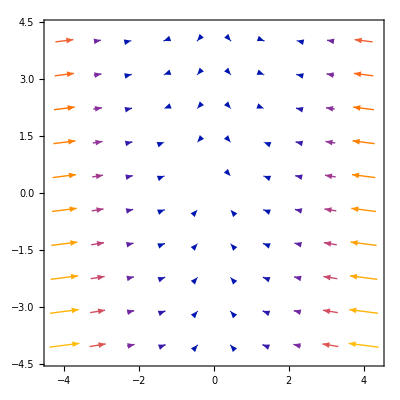

```mathematica
VP2=VectorPlot[-gradF2,{x1,-4,4},{x2,-4,4},ColorFunction->ColorData["AlpineColors"],VectorScale->Automatic,VectorPoints->10]
```

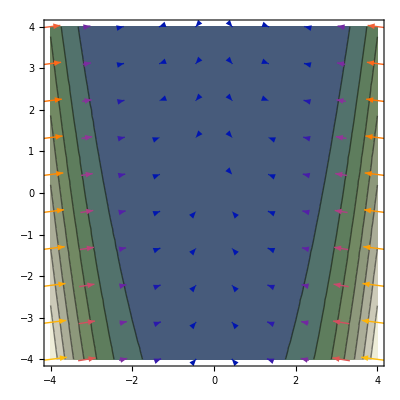

```mathematica
Show[CP2,VP2]
```